#### Configuration

```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
$Assumptions=0<eps<1 && 0<M<1 &&pm>0&&pp>0&& 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&u∈Reals&&u=!=0&&km∈Reals&&0≤ x≤ 1&&0≤ y≤ 1&&0≤ z≤ 1&&0≤ w≤ 1/3&&p3p∈Reals&&p3m∈Reals&&p4p∈Reals&&p4m∈Reals&&lambda∈Reals&&Q>0&&1/3>tau>beta>0&&m∈Integers&&n∈Integers&&n≥0&&m≥0&&muMS>0&&1/3>tau>delta>0&&0<beta<v<1-beta;

turnOffConditional[];

measure=(1-u)u^2

norm00[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->0/.beta->0
norm01[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->0/.beta->1


norm10[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->1/.beta->0
norm11[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->1/.beta->1
norm12[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->1/.beta->2
norm13[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->1/.beta->3

norm21[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->2/.beta->1

norm31[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->3/.beta->1

psi[n_,u_]:=JacobiP[n,1,2,2*u-1]/Sqrt[norm12[n]]


plusDistExpand[e_]:=Module[{f,q,qprime,temp,oldPlus,oldPlusFormal,newPlus,newPlusFormal,newPlusNewQ,newPlusNewQFormal,int1,int2,int3,int4,int5,solution,replaceOLDDEFwiththis,returnMe,isItOLDDEF=1},

  
f=SeriesCoefficient[e,{PlusDistribution[_]^OLDDEF,0,1}];

If[f===0,

Print["Couldn't find an old plus distribution."];
f=SeriesCoefficient[e,{PlusDistribution[_],0,1}];
If[f==0,
Print["No Plus Function Found, Exiting...\n"];
Return[e];
];
isItOLDDEF=0;
q=((e//Expand)/.(f_*PlusDistribution[a_]+x_):>a)/.(f_*PlusDistribution[a_]):>a/.PlusDistribution[a_]:>a/.b_*HeavisideTheta[u-v]+c_:>b/.ubar->1-u/.vbar->1-v;

,(* else *)

Print["Old plus distribution found."];
(* let's extract the q(u,v) and retrieve the formal definition *)
q=((e//Expand)/.(f_*PlusDistribution[a_]^OLDDEF+x_):>a)/.(f_*PlusDistribution[a_]^OLDDEF):>a/.PlusDistribution[a_]^OLDDEF:>a/.b_*HeavisideTheta[u-v]+c_:>b/.ubar->1-u/.vbar->1-v;


];
Print["Our f(u,v) = ", f];
Print["Our q(u,v) = ", q];
int1=Integrate[q/.u->w,{w,1+v,u},Assumptions->0<v<u<1]/.u->v+beta/.ubar->vbar/.v-1->-vbar;
int2=Integrate[q/.v->w/.u->v,{w,0,u},Assumptions->beta<u<v]/.u->v-beta/.ubar->vbar/.v-1->-vbar;
oldPlus=PlusDistribution[q*HeavisideTheta[u-v]+(q/.ubar->UBAR/.u->UU/.vbar->ubar/.v->u/.UBAR->vbar/.UU->v)*HeavisideTheta[v-u]]^OLDDEF;
oldPlusFormal=q*HeavisideTheta[u-v-beta]+(q/.ubar->UBAR/.u->UU/.vbar->ubar/.v->u/.UBAR->vbar/.UU->v)*HeavisideTheta[v-u-beta]+DiracDelta[u-v]*(int1-int2)//FullSimplify//Expand;
Print["The old plus function is as follows:"];
Print[oldPlus," = ",oldPlusFormal,"\n"];


(* to retrieve the new definition, we simply need to subtract the integral of q from 1 to 1+v *)
int3=Integrate[q/.u->w,{w,1,1+v},Assumptions->0<v<u<1]/.u->v+beta/.ubar->vbar/.v-1->-vbar/. 1-v->vbar;
Print[int3];
newPlus=PlusDistribution[q*HeavisideTheta[u-v]+(q/.ubar->UBAR/.u->UU/.vbar->ubar/.v->u/.UBAR->vbar/.UU->v)*HeavisideTheta[v-u]];
newPlusFormal=Collect2[(oldPlusFormal+DiracDelta[u-v]*int3)//expLogs//Expand,DiracDelta[_]]//FullSimplify;
Print["The conversion to the new definition reads:"];
Print[oldPlus," = ",newPlus-DiracDelta[u-v]*int3];
Print["where now"];
Print[newPlus," = ",newPlusFormal,"\n"];


replaceOLDDEFwiththis=newPlusFormal-isItOLDDEF*DiracDelta[u-v]*int3;

Print["Replacing old plus distribution with ", replaceOLDDEFwiththis];

returnMe=(e/.PlusDistribution[_]->replaceOLDDEFwiththis)/.OLDDEF->1;


Return[returnMe];
];
```

(1-u) u^2

```mathematica
normN1N1[n_]:=2^(1+alpha+beta-4)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->-1/.beta->-1
normN1N1[3]
JacobiP[4,-1,-1,u]
```

1/240

15/16 (u-1)^4+15/4 (u-1)^3+9/2 (u-1)^2+(3 (u-1))/2

```mathematica
PlusDistribution[HeavisideTheta[u-v]/(u-v)+HeavisideTheta[v-u]/(v-u)]
plusDistExpand[%]
```

((u-v)/(u-v)+(v-u)/(v-u))_+

Couldn't find an old plus distribution.

Our f(u,v) = 1

Our q(u,v) = 1/(u-v)

The old plus function is as follows:

((u-v)/(u-v)+(v-u)/(v-u))_+^OLDDEF = (u-v-β)/(u-v)-(-u+v-β)/(u-v)+u-v log(β^2/v)

-log(v̄)

The conversion to the new definition reads:

((u-v)/(u-v)+(v-u)/(v-u))_+^OLDDEF = u-v log(v̄)+((u-v)/(u-v)+(v-u)/(v-u))_+

where now

((u-v)/(u-v)+(v-u)/(v-u))_+ = (u-v-β--u+v-β)/(u-v)-u-v log((v v̄)/β^2)

Replacing old plus distribution with (u-v-β--u+v-β)/(u-v)-u-v log((v v̄)/β^2)

(u-v-β--u+v-β)/(u-v)-u-v log((v̄ v)/β^2)

```mathematica
c1a[u_]:=u*(1+2)/(3*u)
c1c[u_]:=1/(u)

c1a[(1+xi)/2]
c1c[(1+xi)/2]
```

1

2/(ξ+1)

```mathematica
JacobiP[1,1,0,xi]
```

1/2 (3 ξ+1)

```mathematica
Integrate[JacobiP[0,1,0,xi]*(1-xi),{xi,-1,1}]
```

2

```mathematica
norm10[3]
```

1/2

```mathematica
nnn=4
alphaa=1
betaa=1

JacobiP[nnn,alphaa,betaa,xi]*JacobiP[nnn,alphaa,betaa,xi]*(1-xi)^alphaa*(1+xi)^betaa
Integrate[%,{xi,-1,1}]

norm11[nnn_]:=2^(1+alphaa+betaa)*Gamma[1+nnn+alphaa]*Gamma[1+betaa+nnn]/(Factorial[nnn]*Gamma[1+alphaa+betaa+nnn]*(1+alphaa+betaa+2*nnn))
```

4

1

1

(105/8 (ξ-1)^4+105/2 (ξ-1)^3+70 (ξ-1)^2+35 (ξ-1)+5)^2 (1-ξ) (ξ+1)

20/33

```mathematica
coeff0=Integrate[c1a[(1+xi)/2]*(1-xi)*JacobiP[0,1,0,xi],{xi,-1,1}]/norm10[0]
coeff1=Integrate[c1a[(1+xi)/2]*(1-xi)*JacobiP[1,1,0,xi],{xi,-1,1}]/norm10[1]
coeff2=Integrate[c1a[(1+xi)/2]*(1-xi)*JacobiP[2,1,0,xi],{xi,-1,1}]/norm10[2]
coeff3=Integrate[c1a[(1+xi)/2]*(1-xi)*JacobiP[3,1,0,xi],{xi,-1,1}]/norm10[3]
coeff4=Integrate[c1a[(1+xi)/2]*(1-xi)*JacobiP[4,1,0,xi],{xi,-1,1}]/norm10[4]
coeff5=Integrate[c1a[(1+xi)/2]*(1-xi)*JacobiP[5,1,0,xi],{xi,-1,1}]/norm10[5]
coeff6=Integrate[c1a[(1+xi)/2]*(1-xi)*JacobiP[6,1,0,xi],{xi,-1,1}]/norm10[6]
```

3/2

0

0

0

«3 more identical outputs»

```mathematica
JacobiP[0,3,3,xi]
JacobiP[1,3,3,xi]
JacobiP[2,1,0,xi]
JacobiP[3,1,0,xi]
```

1

4 ξ

5/2 (ξ-1)^2+6 (ξ-1)+3

35/8 (ξ-1)^3+15 (ξ-1)^2+15 (ξ-1)+4

```mathematica
coeff0=Integrate[c1c[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[0,1,1,xi],{xi,-1,1}]/norm11[0]
coeff1=Integrate[c1c[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[1,1,1,xi],{xi,-1,1}]/norm11[1]
coeff2=Integrate[c1c[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[2,1,1,xi],{xi,-1,1}]/norm11[2]
coeff3=Integrate[c1c[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[3,1,1,xi],{xi,-1,1}]/norm11[3]
coeff4=Integrate[c1c[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[4,1,1,xi],{xi,-1,1}]/norm11[4]
coeff5=Integrate[c1c[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[5,1,1,xi],{xi,-1,1}]/norm11[5]
coeff6=Integrate[c1c[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[6,1,1,xi],{xi,-1,1}]/norm11[6]
```

3

$Aborted

$Aborted

$Aborted

«3 more identical outputs»

```mathematica
Series[coeff0,{eps,0,0}]//Normal

Series[coeff1,{eps,0,0}]//Normal

Series[coeff2,{eps,0,0}]//Normal
```

-3 log(ϵ)-(3 ⅈ π)/2-3

(15 log(ϵ))/4+(15 ⅈ π)/8+75/8

-(14 log(ϵ))/3-(7 ⅈ π)/3-140/9

#### Making sure Jacboi Polynomials Reproduce 1/u

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

2

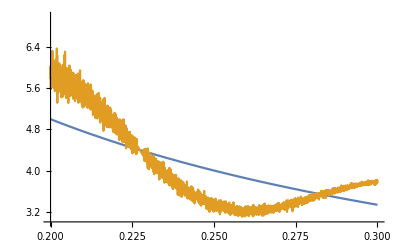

```mathematica
func[u_]:=1/u;
approxFunc=0;


(* decompose func into (0,1) jacobi polynomials up to degree 10 *)

Nmax=23;
norm01[n_]:=2^(1+alpha+beta)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->0/.beta->1

coeffArrStartAtOne=ConstantArray[0,Nmax]

coeff0=Integrate[func[(1+xi)/2]*(1+xi)*JacobiP[0,0,1,xi],{xi,-1,1}]/norm01[0];
approxFunc=coeff0*JacobiP[0,0,1,2u-1]

i=1;
For[i=1,i≤Nmax,i++,
coeffArrStartAtOne[[i]]=Integrate[func[(1+xi)/2]*(1+xi)*JacobiP[i,0,1,xi],{xi,-1,1}]/norm01[i];
(*Print[coeffArrStartAtOne[[i]]];*)
approxFunc+=coeffArrStartAtOne[[i]]*JacobiP[i,0,1,2u-1];
];

Plot[{func[u],approxFunc},{u,0.2,0.3},PlotRange->{3,7}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

2

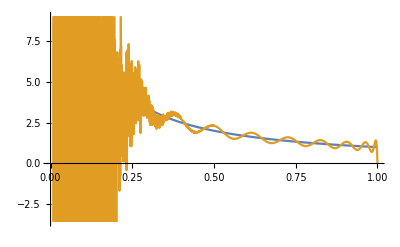

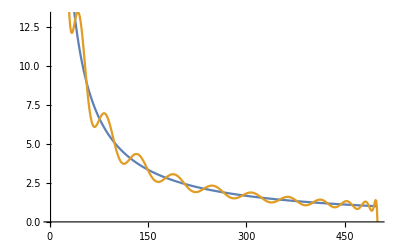

495918532948104 u^25-6446940928325352 u^24+39503314511797500 u^23-151692727725302400 u^22+409415576360637600 u^21-825654745660619160 u^20+1291183485235223580 u^19-1603954640043756000 u^18+1608410069599433100 u^17-1315971875126808900 u^16+884455516073599470 u^15-490087905010479360 u^14+224125566315768000 u^13-84478098072866400 u^12+26147982736839600 u^11-6605806165096320 u^10+1350173219555160 u^9-220616539143000 u^8+28364983604100 u^7-2810153174400 u^6+208632584160 u^5-11176745580 u^4+409704750 u^3-9500400 u^2+122850 u+1/u-702

u (495918532948104 u^25-6446940928325352 u^24+39503314511797500 u^23-151692727725302400 u^22+409415576360637600 u^21-825654745660619160 u^20+1291183485235223580 u^19-1603954640043756000 u^18+1608410069599433100 u^17-1315971875126808900 u^16+884455516073599470 u^15-490087905010479360 u^14+224125566315768000 u^13-84478098072866400 u^12+26147982736839600 u^11-6605806165096320 u^10+1350173219555160 u^9-220616539143000 u^8+28364983604100 u^7-2810153174400 u^6+208632584160 u^5-11176745580 u^4+409704750 u^3-9500400 u^2+122850 u+1/u-702)

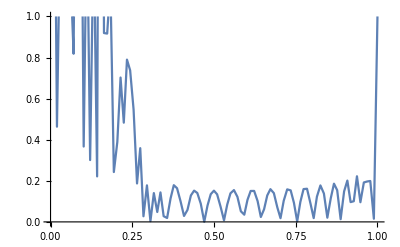

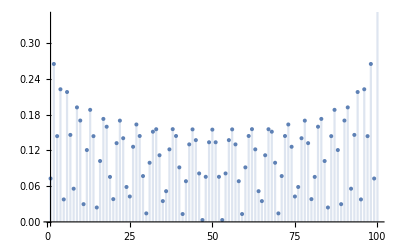

```mathematica
func[u_]:=1/u;
approxFunc=0;


(* decompose func into (0,1) jacobi polynomials up to degree 10 *)

Nmax=25;
norm01[n_]:=2^(1+alpha+beta)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->0/.beta->1

coeffArrStartAtOne=ConstantArray[0,Nmax]

coeff0=Integrate[func[(1+xi)/2]*(1+xi)*JacobiP[0,0,1,xi],{xi,-1,1}]/norm01[0];
approxFunc=coeff0*JacobiP[0,0,1,2u-1]

i=1;
For[i=1,i≤Nmax,i++,
coeffArrStartAtOne[[i]]=Integrate[func[(1+xi)/2]*(1+xi)*JacobiP[i,0,1,xi],{xi,-1,1}]/norm01[i];
(*Print[coeffArrStartAtOne[[i]]];*)
approxFunc+=coeffArrStartAtOne[[i]]*JacobiP[i,0,1,2u-1];
];

(* the function and its approximator -- continuous version*)
Plot[{func[u],approxFunc},{u,0,1}]

(* the function and its approximator -- discrete version*)
DiscretePlot[{func[n/500],approxFunc/.u->n/500},{n,1,500},Filling->None,Joined->True]

diff=Expand[(func[u]-approxFunc)]
percentdiff=Expand[(func[u]-approxFunc)]/func[u]
Plot[Abs[(func[u]-approxFunc)/func[u]],{u,0,1},PlotRange->{0,1},MaxRecursion->1]



percentDiffAtHundredths=ConstantArray[0,100];

For[i=1,i≤100,i++,
percentDiffAtHundredths[[i]]=percentdiff/.u->i/100;
]

DiscretePlot[Abs@percentDiffAtHundredths[[n]],{n,1,100}]
```

(ⅇ^(-ⅈ x) (-π-π+2 ⅈ π))/(2 π)-(ⅇ^(ⅈ x) (-π-π+2 ⅈ π))/(2 π)+(ⅈ (2 2 π+π) ⅇ^(-2 ⅈ x))/(2 π)-(ⅈ (2 2 π+π) ⅇ^(2 ⅈ x))/(2 π)+(ⅈ (2 3 π+π) ⅇ^(-3 ⅈ x))/(2 π)-(ⅈ (2 3 π+π) ⅇ^(3 ⅈ x))/(2 π)+(ⅈ (2 4 π+π) ⅇ^(-4 ⅈ x))/(2 π)-(ⅈ (2 4 π+π) ⅇ^(4 ⅈ x))/(2 π)+(ⅈ (2 5 π+π) ⅇ^(-5 ⅈ x))/(2 π)-(ⅈ (2 5 π+π) ⅇ^(5 ⅈ x))/(2 π)+(ⅈ (2 6 π+π) ⅇ^(-6 ⅈ x))/(2 π)-(ⅈ (2 6 π+π) ⅇ^(6 ⅈ x))/(2 π)+(ⅈ (2 7 π+π) ⅇ^(-7 ⅈ x))/(2 π)-(ⅈ (2 7 π+π) ⅇ^(7 ⅈ x))/(2 π)+(ⅈ (2 8 π+π) ⅇ^(-8 ⅈ x))/(2 π)-(ⅈ (2 8 π+π) ⅇ^(8 ⅈ x))/(2 π)+(ⅈ (2 9 π+π) ⅇ^(-9 ⅈ x))/(2 π)-(ⅈ (2 9 π+π) ⅇ^(9 ⅈ x))/(2 π)+(ⅈ (2 10 π+π) ⅇ^(-10 ⅈ x))/(2 π)-(ⅈ (2 10 π+π) ⅇ^(10 ⅈ x))/(2 π)+(ⅈ (2 11 π+π) ⅇ^(-11 ⅈ x))/(2 π)-(ⅈ (2 11 π+π) ⅇ^(11 ⅈ x))/(2 π)+(ⅈ (2 12 π+π) ⅇ^(-12 ⅈ x))/(2 π)-(ⅈ (2 12 π+π) ⅇ^(12 ⅈ x))/(2 π)+(ⅈ (2 13 π+π) ⅇ^(-13 ⅈ x))/(2 π)-(ⅈ (2 13 π+π) ⅇ^(13 ⅈ x))/(2 π)+(ⅈ (2 14 π+π) ⅇ^(-14 ⅈ x))/(2 π)-(ⅈ (2 14 π+π) ⅇ^(14 ⅈ x))/(2 π)+(ⅈ (2 15 π+π) ⅇ^(-15 ⅈ x))/(2 π)-(ⅈ (2 15 π+π) ⅇ^(15 ⅈ x))/(2 π)

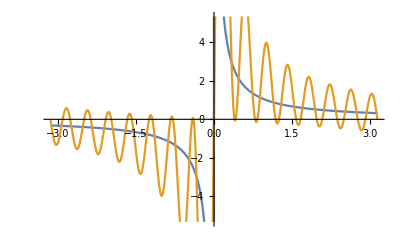

```mathematica
FourierSeries[1/(x),x,15]
Plot[{1/(x),%},{x,-Pi,Pi}]
```

```mathematica
D[a^x,x]
```

a^x log(a)

```mathematica
FourierSr
```

(ⅇ^(-ⅈ x) (-π-π+2 ⅈ π))/(2 π)-(ⅇ^(ⅈ x) (-π-π+2 ⅈ π))/(2 π)+(ⅈ (2 2 π+π) ⅇ^(-2 ⅈ x))/(2 π)-(ⅈ (2 2 π+π) ⅇ^(2 ⅈ x))/(2 π)+(ⅈ (2 3 π+π) ⅇ^(-3 ⅈ x))/(2 π)-(ⅈ (2 3 π+π) ⅇ^(3 ⅈ x))/(2 π)

yt

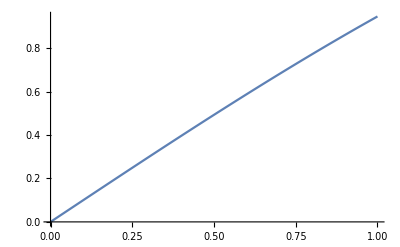

```mathematica
Integrate[Sin[x]/x,{x,0,yt}]
Plot[%,{yt,0,1}]
```

```mathematica
Factorial[3]
Gamma[3+1]
```

6

6

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

6

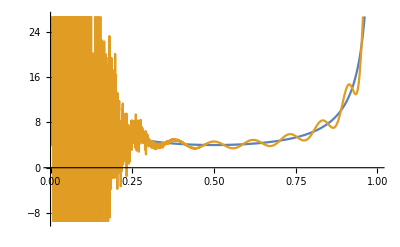

Power::infy: Infinite expression TraditionalForm`1/0 encountered.

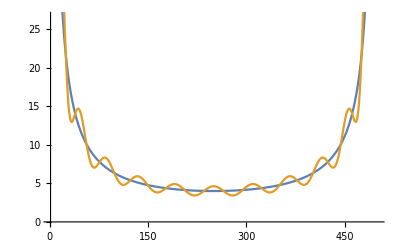

-495918532948104 u^24+5951022395377248 u^23-33552292116420252 u^22+118140435608882148 u^21-291275140751755452 u^20+534379604908863708 u^19-756803880326359872 u^18+847150759717396128 u^17-761259309882036972 u^16+554712565244771928 u^15-329742950828827542 u^14+160344954181651818 u^13-63780612134116182 u^12+20697485938750218 u^11-5450496798089382 u^10+1155309367006938 u^9-194863852548222 u^8+25752686594778 u^7-2612297009322 u^6+197856165078 u^5-10776419082 u^4+400326498 u^3-9378252 u^2+122148 u+1/((1-u) u)-702

(1-u) u (-495918532948104 u^24+5951022395377248 u^23-33552292116420252 u^22+118140435608882148 u^21-291275140751755452 u^20+534379604908863708 u^19-756803880326359872 u^18+847150759717396128 u^17-761259309882036972 u^16+554712565244771928 u^15-329742950828827542 u^14+160344954181651818 u^13-63780612134116182 u^12+20697485938750218 u^11-5450496798089382 u^10+1155309367006938 u^9-194863852548222 u^8+25752686594778 u^7-2612297009322 u^6+197856165078 u^5-10776419082 u^4+400326498 u^3-9378252 u^2+122148 u+1/((1-u) u)-702)

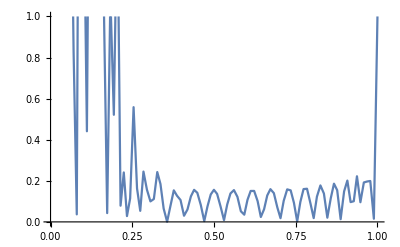

Power::infy: Infinite expression TraditionalForm`1/0 encountered.

Infinity::indet: Indeterminate expression TraditionalForm`0\ ComplexInfinity encountered.

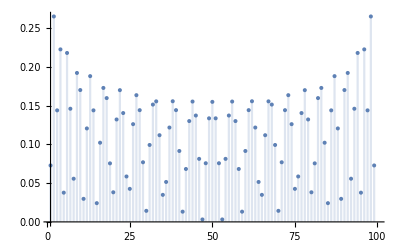

```mathematica
func[u_]:=1/((1-u)*u);
approxFunc=0;


(* decompose func into (0,1) jacobi polynomials up to degree 10 *)

Nmax=25;
norm11[n_]:=2^(1+alpha+beta)*Gamma[1+n+alpha]*Gamma[1+beta+n]/(Factorial[n]*Gamma[1+alpha+beta+n]*(1+alpha+beta+2*n))/.alpha->1/.beta->1

coeffArrStartAtOne=ConstantArray[0,Nmax]

coeff0=Integrate[func[(1+xi)/2]*(1-xi)^1*(1+xi)*JacobiP[0,1,1,xi],{xi,-1,1}]/norm11[0];
approxFunc=coeff0*JacobiP[0,1,1,2u-1]

i=1;
For[i=1,i≤Nmax,i++,
coeffArrStartAtOne[[i]]=Integrate[func[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[i,1,1,xi],{xi,-1,1}]/norm11[i];
(*Print[coeffArrStartAtOne[[i]]];*)
approxFunc+=coeffArrStartAtOne[[i]]*JacobiP[i,1,1,2u-1];
];

(* the function and its approximator -- continuous version*)
Plot[{func[u],approxFunc},{u,0,1}]

(* the function and its approximator -- discrete version*)
DiscretePlot[{func[n/500],approxFunc/.u->n/500},{n,1,500},Filling->None,Joined->True]

diff=Expand[(func[u]-approxFunc)]
percentdiff=Expand[(func[u]-approxFunc)]/func[u]
Plot[Abs[(func[u]-approxFunc)/func[u]],{u,0,1},PlotRange->{0,1},MaxRecursion->1]



percentDiffAtHundredths=ConstantArray[0,100];

For[i=1,i≤100,i++,
percentDiffAtHundredths[[i]]=percentdiff/.u->i/100;
]

DiscretePlot[Abs@percentDiffAtHundredths[[n]],{n,1,100}]
```

```mathematica
symFunc[x,y]
```

(-x-y+1)/((1-x)^2 (1-y)^2)

```mathematica
psi[0,u]
psi[1,u]
psi[2,u]
psi[3,u]
```

2 √3

√3 (5 (2 u-1)+1)

2 √(10/3) (21/4 (2 u-2)^2+12 (2 u-2)+6)

√15 (21/2 (2 u-2)^3+35 (2 u-2)^2+35 (2 u-2)+10)

```mathematica
coeff0=Integrate[measure*symFunc[u,v]psi[0,u],{u,0,1}]//FullSimplify
coeff1=Integrate[measure*symFunc[u,v]psi[1,u],{u,0,1}]//FullSimplify
coeff2=Integrate[measure*symFunc[u,v]psi[2,u],{u,0,1}]//FullSimplify
coeff3=Integrate[measure*symFunc[u,v]psi[3,u],{u,0,1}]//FullSimplify
coeff4=Integrate[measure*symFunc[u,v]psi[4,u],{u,0,1}]//FullSimplify


Integrate[(measure/.u->v)*coeff0*psi[0,v],{v,0,1}]
Integrate[(measure/.u->v)*coeff0*psi[1,v],{v,0,1}]
Integrate[(measure/.u->v)*coeff0*psi[2,v],{v,0,1}]
Integrate[(measure/.u->v)*coeff0*psi[3,v],{v,0,1}]
Integrate[(measure/.u->v)*coeff0*psi[4,v],{v,0,1}]
```

√3

(4-10 v)/(√3)

√(15/2) (v (7 v-6)+1)

-2 √(3/5) (7 v (6 v^2-8 v+3)-2)

$Aborted

$Aborted

$Aborted

«3 more identical outputs»

```mathematica
Integrate[JacobiP[1,2,2,xi]*JacobiP[1,2,2,xi]]
```

{0,0,0,0,0}

3/4 ∫_-1^1 (1-ξ) (ξ+1) symFunc((ξ+1)/2)ⅆξ

NIntegrate::inumr: The integrand TraditionalForm`(1 - ξ)\ (1 + ξ)\ symFunc(1 + ξ/2) has evaluated to non-numerical values for all sampling points in the region with boundaries \!
\(TraditionalForm\`\(( \*GridBox[{{\(-1\), "1"}}, RowSpacings -> 1, ColumnSpacings -> 1, RowAlignments -> Baseline, 
       ColumnAlignments -> Center] )\)\)
.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

$Aborted

$Aborted

$Aborted

«3 more identical outputs»

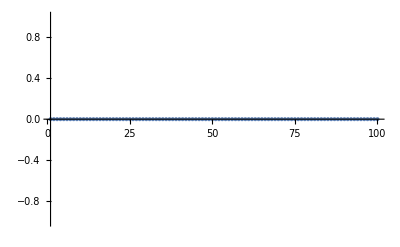

```mathematica
(* checking that symmetric functions can be decomposed to give eigrenvalue equations *)



approxFunc=0;


(* decompose func into (0,1) jacobi polynomials up to degree 10 *)

Nmax=5;


coeffArrStartAtOne=ConstantArray[0,Nmax]

coeff0=Integrate[symFunc[(1+xi)/2]*(1-xi)^1*(1+xi)*JacobiP[0,1,1,xi],{xi,-1,1}]/norm11[0];
approxFunc=coeff0*JacobiP[0,1,1,2u-1]

i=1;
For[i=1,i≤Nmax,i++,
coeffArrStartAtOne[[i]]=Integrate[symFunc[(1+xi)/2]*(1-xi)*(1+xi)*JacobiP[i,1,1,xi],{xi,-1,1}]/norm11[i];
(*Print[coeffArrStartAtOne[[i]]];*)
approxFunc+=coeffArrStartAtOne[[i]]*JacobiP[i,1,1,2u-1];
];

(* the function and its approximator -- continuous version*)
Plot[{func[u],approxFunc},{u,0,1}]

(* the function and its approximator -- discrete version*)
DiscretePlot[{func[n/500],approxFunc/.u->n/500},{n,1,500},Filling->None,Joined->True]

diff=Expand[(func[u]-approxFunc)]
percentdiff=Expand[(func[u]-approxFunc)]/func[u]
Plot[Abs[(func[u]-approxFunc)/func[u]],{u,0,1},PlotRange->{0,1},MaxRecursion->1]



percentDiffAtHundredths=ConstantArray[0,100];

For[i=1,i≤100,i++,
percentDiffAtHundredths[[i]]=percentdiff/.u->i/100;
]

DiscretePlot[Abs@percentDiffAtHundredths[[n]],{n,1,100}]
```

#### Checking for Conformality of Anomalopus Dimensions -- 1e

```mathematica
psi[n_,u_]:=JacobiP[n,3,1,2*u-1]/Sqrt[norm11[n]]
```

```mathematica
answerDiag=Cf/2+Ca(LQ^2+Log[v]-1)
answerCfa=-(1/(v*vbar))(v*ubar*UnitStep[u-v]+u*vbar*UnitStep[v-u]+PlusDistribution[ubar*v*HeavisideTheta[u-v]/(u-v)+u*vbar*HeavisideTheta[v-u]/(v-u)])
totalAnswer=answerDiag*DiracDelta[u-v]+answerCfa*(Cf-Ca/2)

Wuv=SeriesCoefficient[totalAnswer/.DiracDelta[_]->DIRACDELTA,{DIRACDELTA,0,1}]
Vuv=((totalAnswer-Wuv*DiracDelta[u-v])/(u*ubar)//plusDistExpand)
```

C_A (LQ^2+log(v)-1)+C_F/2

-(((ū v u-v)/(u-v)+(v̄ u v-u)/(v-u))_++ū v u-v+v̄ u v-u)/(v̄ v)

u-v (C_A (LQ^2+log(v)-1)+C_F/2)-((C_F-C_A/2) (((ū v u-v)/(u-v)+(v̄ u v-u)/(v-u))_++ū v u-v+v̄ u v-u))/(v̄ v)

LQ^2 C_A+C_A log(v)-C_A+C_F/2

Couldn't find an old plus distribution.

Our f(u,v) = (C_A-2 C_F)/(2 u ū v v̄)

Our q(u,v) = ((1-u) v)/(u-v)

Integrate::idiv: Integral of TraditionalForm`v\ w/w - v - w/w - v does not converge on TraditionalForm`{0, u}.

The old plus function is as follows:

(((1-u) v u-v)/(u-v)+(u (1-v) v-u)/(v-u))_+^OLDDEF = v u-v+v v̄ u-v-v β u-v-v̄ β u-v-v v̄ log(v/β^2) u-v-(u v u-v-β)/(u-v)+(v u-v-β)/(u-v)+(u v -u+v-β)/(u-v)-(u -u+v-β)/(u-v)

v (-v̄ log(v̄)-v)

The conversion to the new definition reads:

(((1-u) v u-v)/(u-v)+(u (1-v) v-u)/(v-u))_+^OLDDEF = (((1-u) v u-v)/(u-v)+(u (1-v) v-u)/(v-u))_+-v u-v (-v-v̄ log(v̄))

where now

(((1-u) v u-v)/(u-v)+(u (1-v) v-u)/(v-u))_+ = ((v-u v) u-v-β+u (v-1) -u+v-β)/(u-v)+u-v (v (-v+v̄+1)-(v+v̄) β-v v̄ log((v v̄)/β^2))

Replacing old plus distribution with ((v-u v) u-v-β+u (v-1) -u+v-β)/(u-v)+u-v (v (-v+v̄+1)-(v+v̄) β-v v̄ log((v v̄)/β^2))

(-((C_F-C_A/2) (u-v (-v̄ v log((v̄ v)/β^2)-β (v̄+v)+v (v̄-v+1))+((v-u v) u-v-β+u (v-1) -u+v-β)/(u-v)+ū v u-v+v̄ u v-u))/(v̄ v)-u-v (LQ^2 C_A+C_A log(v)-C_A+C_F/2)+u-v (C_A (LQ^2+log(v)-1)+C_F/2))/(ū u)

```mathematica
Vuv//Expand
%//FullSimplify
igrand=ubar*u*(%)*psi[0,u]/.ubar->1-u/.vbar->1-v/.Ca->0/.Cf->1
%//FullSimplify
igral=Integrate[%,{u,0,1}]
```

-(C_A u-v log((v̄ v)/β^2))/(2 ū u)-(β C_A u-v)/(2 ū v̄ u)-(v C_A u-v)/(2 ū v̄ u)+(C_A u-v)/(2 ū v̄ u)-(β C_A u-v)/(2 ū u v)+(C_A u-v)/(2 ū u)-(C_A u-v-β)/(2 ū v̄ (u-v))+(C_A u-v-β)/(2 ū v̄ u (u-v))+(C_A -u+v-β)/(2 ū v̄ (u-v))-(C_A -u+v-β)/(2 ū v̄ v (u-v))+(C_A v-u)/(2 ū v)+(C_A u-v)/(2 v̄ u)+(C_F u-v log((v̄ v)/β^2))/(ū u)+(β C_F u-v)/(ū v̄ u)+(v C_F u-v)/(ū v̄ u)-(C_F u-v)/(ū v̄ u)+(β C_F u-v)/(ū u v)-(C_F u-v)/(ū u)+(C_F u-v-β)/(ū v̄ (u-v))-(C_F u-v-β)/(ū v̄ u (u-v))-(C_F -u+v-β)/(ū v̄ (u-v))+(C_F -u+v-β)/(ū v̄ v (u-v))-(C_F v-u)/(ū v)-(C_F u-v)/(v̄ u)

-(C_A u-v log((v̄ v)/β^2))/(2 ū u)-(β C_A u-v)/(2 ū v̄ u)-(v C_A u-v)/(2 ū v̄ u)+(C_A u-v)/(2 ū v̄ u)-(β C_A u-v)/(2 ū u v)+(C_A u-v)/(2 ū u)+((C_A-2 C_F) ((v-u v) u-v-β+u (v-1) -u+v-β+(u-v) (ū v u-v+v̄ u v-u)))/(2 ū v̄ u v (u-v))+(C_F u-v log((v̄ v)/β^2))/(ū u)+(β C_F u-v)/(ū v̄ u)+(v C_F u-v)/(ū v̄ u)-(C_F u-v)/(ū v̄ u)+(β C_F u-v)/(ū u v)-(C_F u-v)/(ū u)

2 √3 (1-u) u ((u-v log(((1-v) v)/β^2))/((1-u) u)+(β u-v)/((1-u) u (1-v))+(β u-v)/((1-u) u v)+(v u-v)/((1-u) u (1-v))-(u-v)/((1-u) u)-(u-v)/((1-u) u (1-v))-((v-u v) u-v-β+u (v-1) -u+v-β+(u-v) ((1-u) v u-v+u (1-v) v-u))/((1-u) u (1-v) v (u-v)))

-2 √3 (u-1) u ((u-v log(((1-v) v)/β^2))/(u-u^2)+(β u-v)/(u v-u^2 v)+(β u-v)/((u-1) u (v-1))+(v u-v)/((u-1) u (v-1))+(u-v)/((u-1) u)+(u-v)/(u (u (-v)+u+v-1))+((u-1) v u-v-β+(u-u v) -u+v-β+(u-v) ((u-1) v u-v+u (v-1) v-u))/((u-1) u (v-1) v (u-v)))

(2 √3 (2 v-1))/((v-1) v)

```mathematica
igral/.beta->0//FullSimplify
```

(2 √3 (2 v-1))/((v-1) v)

```mathematica
igral/.beta->0//FullSimplify
%/psi[0,v]//FullSimplify
psi[0,v]
```

(√10 (4 v-1))/((v-1) v)

1/v+3/(v-1)

√10

#### Checking for Conformality in 1an AnomDim

```mathematica
psi[n_,u_]:=JacobiP[n,1,2,2*u-1]/Sqrt[norm12[n]]
```

```mathematica
answerDiag=Cf(LQ^2-3/2+Log[vbar])+Ca/2
answerCfa=ubar(u*v*UnitStep[1-u-v]/(ubar*vbar)+(u*v+u+v-1)*UnitStep[u+v-1]/(u*v))
(* Assuming Ray and Simon used the old definition *)
(*answerCa=(-1/2)ubar((vbar-u*v)UnitStep[u-v]/(u*vbar)+(ubar-u*v)UnitStep[v-u]/(v*ubar)+PlusDistribution[ubar*HeavisideTheta[u-v]/(u-v)+vbar*HeavisideTheta[v-u]/(v-u)]^OLDDEF/(ubar*vbar))
totalAnswer=answerDiag*DiracDelta[u-v]+answerCfa*(Cf-Ca/2)+answerCa*Ca
Wuv=SeriesCoefficient[totalAnswer,{DiracDelta[_],0,1}]
Vuv=((totalAnswer-Wuv*DiracDelta[u-v])/ubar//plusDistExpand)*)
```

C_A/2+C_F (LQ^2+log(v̄)-3/2)

ū ((u (n+n̄) 1/2 (-n-n̄)-u+1)/(2 ū v̄)+(2 (1/2 u (n+n̄)+(n+n̄)/2+u-1) (n+n̄)/2+u-1)/(u (n+n̄)))

```mathematica
v
```

(n+n̄)/2

```mathematica
Vuv//Expand
igrand=ubar*u^2*(%/(u*v))*psi[1,u]/.ubar->1-u/.vbar->1-v/.Ca->0/.Cf->1
%//FullSimplify
igral=integrateTermByTerm[%,{u,0,1}]
```

(C_A u-v log((v̄ v)/β^2))/(2 ū)+(β C_A u-v)/(2 ū v̄)-(C_A u-v)/(2 ū v̄)-(C_A log(v̄) u-v)/(2 ū)-(C_A u-v-β)/(2 ū v̄ (u-v))+(u C_A u-v-β)/(2 ū v̄ (u-v))-(v C_A -u+v-β)/(2 ū v̄ (u-v))+(C_A -u+v-β)/(2 ū v̄ (u-v))-(u v C_A -u-v+1)/(2 ū v̄)+(u C_A v-u)/(2 ū)+(v C_A u-v)/(2 v̄)-(C_A u-v)/(2 u)-(C_A v-u)/(2 v)-1/2 C_A u+v-1-(C_A u+v-1)/(2 u)-(C_A u+v-1)/(2 v)+(C_A u+v-1)/(2 u v)+(u v C_F -u-v+1)/(ū v̄)+C_F u+v-1+(C_F u+v-1)/u+(C_F u+v-1)/v-(C_F u+v-1)/(u v)

(√3 (1-u) u (5 (2 u-1)-1) ((u v -u-v+1)/((1-u) (1-v))+(u+v-1)/u-(u+v-1)/(u v)+(u+v-1)/v+u+v-1))/v

-(2 √3 (5 u-3) (u^2 v^2 -u-v+1+(u-1) (v-1) (u v+u+v-1) u+v-1))/((v-1) v^2)

Integrating 13 terms.

Term 1 : (6 √3 u^2 -u-v+1)/(v-1)

1 : -2 √3 (v-1)^2

Term 2 : -(10 √3 u^3 -u-v+1)/(v-1)

2 : -5/2 √3 (v-1)^3

Term 3 : -(6 √3 u+v-1)/(v-1)

3 : -(6 √3 v)/(v-1)

Term 4 : (10 √3 u u+v-1)/(v-1)

4 : -(5 √3 (v-2) v)/(v-1)

Term 5 : (6 √3 u^2 u+v-1)/(v-1)

5 : (2 √3 v ((v-3) v+3))/(v-1)

Term 6 : -(10 √3 u^3 u+v-1)/(v-1)

6 : (5 √3 (v-2) v ((v-2) v+2))/(2 (v-1))

Term 7 : -(6 √3 u+v-1)/((v-1) v^2)

7 : (6 √3)/(v-v^2)

Term 8 : (22 √3 u u+v-1)/((v-1) v^2)

8 : -(11 √3 (v-2))/((v-1) v)

Term 9 : -(26 √3 u^2 u+v-1)/((v-1) v^2)

9 : -(26 ((v-3) v+3))/(√3 (v-1) v)

Term 10 : (10 √3 u^3 u+v-1)/((v-1) v^2)

10 : -(5 √3 (v-2) ((v-2) v+2))/(2 (v-1) v)

Term 11 : (12 √3 u+v-1)/((v-1) v)

11 : (12 √3)/(v-1)

Term 12 : -(32 √3 u u+v-1)/((v-1) v)

12 : (16 √3 (v-2))/(v-1)

Term 13 : (20 √3 u^2 u+v-1)/((v-1) v)

13 : (20 ((v-3) v+3))/(√3 (v-1))

(6 √3)/(v-v^2)-5/2 √3 (v-1)^3-2 √3 (v-1)^2+(16 √3 (v-2))/(v-1)-(5 √3 (v-2) v)/(v-1)-(6 √3 v)/(v-1)+(2 √3 v ((v-3) v+3))/(v-1)-(26 ((v-3) v+3))/(√3 v (v-1))+(20 ((v-3) v+3))/(√3 (v-1))+(5 √3 (v-2) v ((v-2) v+2))/(2 (v-1))-(5 √3 (v-2) ((v-2) v+2))/(2 v (v-1))-(11 √3 (v-2))/(v (v-1))+(12 √3)/(v-1)

```mathematica
igral//FullSimplify
%/psi[1,v]//FullSimplify
```

(3-5 v)/(2 √3)

-1/12

#### Checking for Conformality in 2a1 AnomDim

```mathematica
psi[n_,u_]:=JacobiP[n,3,1,2*u-1]/Sqrt[norm31[n]]
```

```mathematica
answerDiag=Cf(LQ^2+Log[vbar]-3/2)+Ca/2(1+Log[v]+(3-4v)/(2vbar^2))
answerCfa=(u*ubar/vbar)(ubar*vbar*UnitStep[u+v-1]/(u*v)+(ubar*vbar+ubar+vbar-1)*UnitStep[1-u-v]/(ubar*vbar))
answerCa=(-1/2)(u*ubar/vbar)(ubar(1+vbar)UnitStep[u-v]/(u*vbar)+vbar*(ubar+1)UnitStep[v-u]/(v*ubar)+PlusDistribution[v*ubar^2*HeavisideTheta[u-v]/(u-v)+u*vbar^2*HeavisideTheta[v-u]/(v-u)]^OLDDEF/(u*ubar*v*vbar))
totalAnswer=answerDiag*DiracDelta[u-v]+answerCfa*(Cf-Ca/2)+answerCa*Ca

Wuv=SeriesCoefficient[totalAnswer,{DiracDelta[_],0,1}]
Vuv=((totalAnswer-Wuv*DiracDelta[u-v])/(ubar^2*u)//plusDistExpand)
```

1/2 C_A ((3-4 v)/(2 (v̄)^2)+log(v)+1)+C_F (LQ^2+log(v̄)-3/2)

(ū u (((ū v̄+ū+v̄-1) -u-v+1)/(ū v̄)+(ū v̄ u+v-1)/(u v)))/(v̄)

-(ū u (((((ū)^2 v u-v)/(u-v)+((v̄)^2 u v-u)/(v-u))_+^OLDDEF)/(ū v̄ u v)+(ū (v̄+1) u-v)/(v̄ u)+((ū+1) v̄ v-u)/(ū v)))/(2 v̄)

u-v (1/2 C_A ((3-4 v)/(2 (v̄)^2)+log(v)+1)+C_F (LQ^2+log(v̄)-3/2))+(ū u (C_F-C_A/2) (((ū v̄+ū+v̄-1) -u-v+1)/(ū v̄)+(ū v̄ u+v-1)/(u v)))/(v̄)-(ū u C_A (((((ū)^2 v u-v)/(u-v)+((v̄)^2 u v-u)/(v-u))_+^OLDDEF)/(ū v̄ u v)+(ū (v̄+1) u-v)/(v̄ u)+((ū+1) v̄ v-u)/(ū v)))/(2 v̄)

-(v C_A)/(v̄)^2+(3 C_A)/(4 (v̄)^2)+1/2 C_A log(v)+C_A/2+LQ^2 C_F+C_F log(v̄)-(3 C_F)/2

Old plus distribution found.

Our f(u,v) = -C_A/(2 u (ū)^2 v (v̄)^2)

Our q(u,v) = ((1-u)^2 v)/(u-v)

Integrate::idiv: Integral of TraditionalForm`w/v - w does not converge on TraditionalForm`{0, u}.

The old plus function is as follows:

((v u-v (1-u)^2)/(u-v)+(u (1-v)^2 v-u)/(v-u))_+^OLDDEF = (v u-v-β u^2)/(u-v)-(2 v u-v-β u)/(u-v)-(v^2 -u+v-β u)/(u-v)+(2 v -u+v-β u)/(u-v)-(-u+v-β u)/(u-v)-2 v^2 u-v+v (v̄)^2 u-v+1/2 v β^2 u-v+(3 v u-v)/2+2 v^2 β u-v-(v̄)^2 β u-v-2 v β u-v+(v u-v-β)/(u-v)+v (v̄)^2 u-v log(β)+v (v̄)^2 u-v log(β/v)

-v ((v̄)^2 log(v̄)-(3 v^2)/2+v)

The conversion to the new definition reads:

((v u-v (1-u)^2)/(u-v)+(u (1-v)^2 v-u)/(v-u))_+^OLDDEF = v u-v (-(3 v^2)/2+v+(v̄)^2 log(v̄))+((v u-v (1-u)^2)/(u-v)+(u (1-v)^2 v-u)/(v-u))_+

where now

((v u-v (1-u)^2)/(u-v)+(u (1-v)^2 v-u)/(v-u))_+ = ((u-1)^2 v u-v-β-u (v-1)^2 -u+v-β)/(u-v)+1/2 u-v (3 v (v-1)^2+2 v (v̄)^2+v β^2+2 (2 (v-1) v-(v̄)^2) β-2 v (v̄)^2 log((v v̄)/β^2))

Replacing old plus distribution with ((u-1)^2 v u-v-β-u (v-1)^2 -u+v-β)/(u-v)+v u-v (-(3 v^2)/2+v+(v̄)^2 log(v̄))+1/2 u-v (3 v (v-1)^2+2 v (v̄)^2+v β^2+2 (2 (v-1) v-(v̄)^2) β-2 v (v̄)^2 log((v v̄)/β^2))

(-u-v (-(v C_A)/(v̄)^2+(3 C_A)/(4 (v̄)^2)+1/2 C_A log(v)+C_A/2+LQ^2 C_F+C_F log(v̄)-(3 C_F)/2)+u-v (1/2 C_A ((3-4 v)/(2 (v̄)^2)+log(v)+1)+C_F (LQ^2+log(v̄)-3/2))-(ū u C_A ((v u-v ((v̄)^2 log(v̄)-(3 v^2)/2+v)+1/2 u-v (-2 (v̄)^2 v log((v̄ v)/β^2)+2 β (2 (v-1) v-(v̄)^2)+2 (v̄)^2 v+β^2 v+3 v (v-1)^2)+((u-1)^2 v u-v-β-u (v-1)^2 -u+v-β)/(u-v))/(ū v̄ u v)+(ū (v̄+1) u-v)/(v̄ u)+((ū+1) v̄ v-u)/(ū v)))/(2 v̄)+(ū u (C_F-C_A/2) (((ū v̄+ū+v̄-1) -u-v+1)/(ū v̄)+(ū v̄ u+v-1)/(u v)))/(v̄))/((ū)^2 u)

```mathematica
Vuv//Expand
igrand=ubar^3*u*(%/Sqrt[ubar*vbar])*psi[1,u]/.ubar->1-u/.vbar->1-v/.Ca->0/.Cf->1
%//FullSimplify
igral=Integrate[%,{u,0,1}]
```

-(β^2 C_A u-v)/(4 (ū)^2 (v̄)^2 u)-(β v C_A u-v)/((ū)^2 (v̄)^2 u)+(β C_A u-v)/((ū)^2 (v̄)^2 u)+(v C_A u-v)/((ū)^2 (v̄)^2 u)-(3 C_A u-v)/(4 (ū)^2 (v̄)^2 u)+(C_A u-v log((v̄ v)/β^2))/(2 (ū)^2 u)-(C_A log(v̄) u-v)/(2 (ū)^2 u)+(β C_A u-v)/(2 (ū)^2 u v)-(C_A u-v)/(2 (ū)^2 u)+(C_A u-v-β)/((ū)^2 (v̄)^2 (u-v))-(u C_A u-v-β)/(2 (ū)^2 (v̄)^2 (u-v))-(C_A u-v-β)/(2 (ū)^2 (v̄)^2 u (u-v))+(v C_A -u+v-β)/(2 (ū)^2 (v̄)^2 (u-v))-(C_A -u+v-β)/((ū)^2 (v̄)^2 (u-v))+(C_A -u+v-β)/(2 (ū)^2 (v̄)^2 v (u-v))+(C_A -u-v+1)/(2 (ū)^2 (v̄)^2)-(C_A -u-v+1)/(2 (ū)^2 v̄)-(C_A v-u)/(2 (ū)^2 v)-(C_A -u-v+1)/(2 ū (v̄)^2)-(C_A -u-v+1)/(2 ū v̄)-(C_A v-u)/(2 ū v)-(C_A u-v)/(2 (v̄)^2 u)-(C_A u-v)/(2 v̄ u)-(C_A u+v-1)/(2 u v)-(C_F -u-v+1)/((ū)^2 (v̄)^2)+(C_F -u-v+1)/((ū)^2 v̄)+(C_F -u-v+1)/(ū (v̄)^2)+(C_F -u-v+1)/(ū v̄)+(C_F u+v-1)/(u v)

(√35 (1-u)^3 u (6 (2 u-1)+2) ((-u-v+1)/((1-u) (1-v))+(-u-v+1)/((1-u)^2 (1-v))+(-u-v+1)/((1-u) (1-v)^2)-(-u-v+1)/((1-u)^2 (1-v)^2)+(u+v-1)/(u v)))/(4 √((1-u) (1-v)))

-(√35 (3 u-1) √((u-1) (v-1)) ((u-1)^2 (v-1)^2 u+v-1+u v (u (v-2)-2 v+2) -u-v+1))/((v-1)^3 v)

(8 √(1-v) (2 √v (2 v^(3/2)+v^2+v-1)-1))/(3 √35 (√v-1) (√v+1)^3)

```mathematica
igral//FullSimplify
%/psi[1,v]//FullSimplify
psi[1,v]//Expand
```

(8 √(1-v) (2 √v (2 v^(3/2)+v^2+v-1)-1))/(3 √35 (√v-1) (√v+1)^3)

(8 √(1-v) (2 √v (2 v^(3/2)+v^2+v-1)-1))/(105 (√v-1) (√v+1)^3 (3 v-1))

3 √35 v-√35

### Trying Fourier series

```mathematica
answerCfa
```

ū ((u (n+n̄) 1/2 (-n-n̄)-u+1)/(2 ū v̄)+(2 (1/2 u (n+n̄)+(n+n̄)/2+u-1) (n+n̄)/2+u-1)/(u (n+n̄)))